```mathematica
w =10^-6;
R=3 w;n=20;
m=6 * 1.66 10^-27;
h=6.626 10^-34;
hb= h/(2Pi);
V=104.52 1000 h;
ω=2 Pi 1000 {26.22,26.22,4.6};
w0={1,1,4}w;
l=Sqrt[hb/(m ω)];
strobe={300,200,400,150,175,175,160,300,500,1000,750,250,0};
lt={9.89,7.01,9.4,.363,2.93,2.66,.844,11.2,9.07,6.44,15.1,14.8,17.9};
expt=Transpose[{strobe,lt}];
k={kx,ky,kz};
r={x,y,z};
rp={xp,yp,zp};
omega=100 1000 2 Pi;
eg=-V/2+hb Total@ω/2;
```

```mathematica
Integrate[Exp[I k.(r-rp)] Exp[-Total[(2/w0+1/(2 l))(r^2+rp^2)]] ,k∈Sphere[{0,0,0},Sqrt[2 m hb omega]/hb]]
```

$Aborted

```mathematica
AllSpace[v_,rlim_]:=Sequence@@Table[{v[[i]],-rlim,rlim},{i,3}];
```

```mathematica
Integrate[Exp[I k.r-Total[r^2]/2],AllSpace[r]]
```

2 √2 ⅇ^(1/2 (-kx^2-ky^2-kz^2)) π^(3/2)

```mathematica
rpint=Integrate[Exp[(-Total[rp^2])/2],AllSpace[rp]]
```

2 √2 π^(3/2)

```mathematica
b=10^-3;rlim=40;
leff=Sqrt[1/(1/w0^2+1/(4 l^2))];
Intgrl[f_]:=
Module[{kint,kf,intreg,omega},
omega=f 1000 2Pi+eg/hb;
kf=leff Sqrt[(2 m omega)/hb];
(*Print@kf;*)
(*intreg=ImplicitRegion[(k/kf).(k/kf)==1,{kx,ky,kz}];*)
(*intreg=Sphere[{0,0,0},kf[[1]]];*)
(*intreg=Ellipsoid[{0,0,0},{kf[[1]],kf[[1]],kf[[1]]}]*)
(*intreg=Ellipsoid[{0,0,0},kf];
kint=Integrate[Exp[-(k.k)/2],k∈intreg];*)
(*kint=b/π NIntegrate[Exp[-(k.k)/2] 1/(((k/kf).(k/kf)-1)^2+b^2),{kx,-rlim,rlim},{ky,-rlim,rlim},{kz,-rlim,rlim}];*)
(*kint=Integrate[Exp[-(k.k)/2],k∈intreg]*)
kint=Pi(Times@@kf √(2 π) Erf[Norm[kf]/(√2)])/Norm[kf] Exp[-Times@@kf[[1;;2]]/2];
(*intreg=Sphere[{0,0,0}];
kint=NIntegrate[Exp[-((k kf).(k kf))/2],k∈intreg];*)
 (2Pi V^2 Times@@(leff/l))/(4 hb(2Pi)^6 Pi^(3/2))1/(hb omega)1/8 8 π^3 kint
]
```

{{100,0.10511},{105,0.192827},{110,0.353746},{115,0.648956},{120,1.19053},{125,2.18406},{130,4.00671},{135,7.35042},{140,13.4845},{145,24.7378},{150,45.3821},{155,83.2547},{160,152.733},{165,280.193},{170,514.022},{175,942.987},{180,1729.94},{185,3173.61},{190,5822.08},{195,10680.8},{200,19594.2},{205,35946.},{210,65943.9},{215,120976.},{220,221934.},{225,407143.},{230,746916.},{235,1.37024×10^6},{240,2.51374×10^6}}

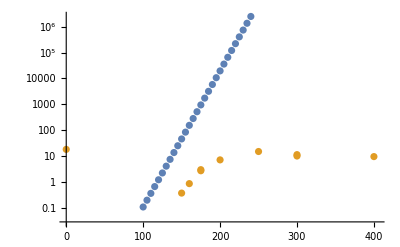

```mathematica
Table[{x,1/Intgrl@x},{x,100,240,5}]
ListLogPlot[{%, expt}]
```

```mathematica
b=10^-3;rlim=40;
leff=Sqrt[1/(1/w0^2+1/(4 l^2))];
Intgrl[f_]:=
Module[{kint,kf,intreg,omega},
omega=f 1000 2Pi+eg/hb;
kf=leff Sqrt[(2 m omega)/hb];
kint=b/π NIntegrate[Exp[-(k.k)/2] 1/(((k/kf).(k/kf)-1)^2+b^2),{kx,-rlim,rlim},{ky,-rlim,rlim},{kz,-rlim,rlim}];
kint=Pi(Times@@kf √(2 π) Erf[Norm[kf]/(√2)])/Norm[kf] Exp[-Times@@kf[[1;;2]]/2];
(*intreg=Sphere[{0,0,0}];
kint=NIntegrate[Exp[-((k kf).(k kf))/2],k∈intreg];*)
 (2Pi V^2 Times@@(leff/l))/(4 hb(2Pi)^6 Pi^(3/2))1/(hb omega)1/8 8 π^3 kint
]
```

{4.52219×10^-7,4.52219×10^-7,1.15861×10^-6}